## Plotting the

```mathematica
spin1={8.5,10.5,12.5,14.5,16.5,18.5,20.5,22.5,24.5,26.5,28.5,30.5,32.5,34.5,36.5,38.5,40.5,42.5,44.5,46.5,48.5};
spin2={13.5,15.5,17.5,19.5,21.5,23.5,25.5,27.5,29.5,31.5,33.5,35.5,37.5,39.5,41.5,43.5,45.5};
spin3={16.5,18.5,20.5,22.5,24.5,26.5,28.5,30.5,32.5,34.5,36.5,38.5,40.5,42.5};
spin4={23.5,25.5,27.5,29.5,31.5,33.5,35.5,37.5,39.5,41.5};
tsd1={0.1966,0.4597,0.7746,1.1609,1.6112,2.1265,2.7051,3.3441,4.0411,4.7937,5.5992,6.457,7.3667,8.3293,9.3458,10.4169,11.5431,12.7224,13.9491,15.2181,16.5221};
tsd2={1.3394,1.7467,2.2184,2.7527,3.3484,4.003,4.7143,5.4805,6.3004,7.1733,8.0998,9.08,10.1147,11.2036,12.3466,13.5441,14.7911};
tsd3={2.1237,2.6293,3.1973,3.8243,4.5094,5.2506,6.0465,6.8963,7.7988,8.7546,9.7638,10.8268,11.9392,13.0861};
tsd4={4.58,5.2251,5.9273,6.6819,7.4919,8.3573,9.2778,10.2535,11.2851,12.3701};
thData={0.239773,0.53694,0.891148,1.30217,1.76987,2.29414,2.87492,3.51215,4.20582,4.95588,5.76232,6.62514,7.54431,8.51984,9.55171,10.6399,11.7845,12.9854,14.2426,15.5561,16.926,1.1397,1.58704,2.0906,2.65028,3.26602,3.93778,4.66556,5.44936,6.2892,7.18508,8.13703,9.14505,10.2092,11.3294,12.5057,13.7382,15.0269,1.8719,2.41133,3.00642,3.65711,4.3634,5.1253,5.94285,6.81608,7.74503,8.72974,9.77026,10.8666,12.0189,13.227,3.85193,4.5738,5.35205,6.18669,7.07768,8.02503,9.02873,10.0888,11.2052,12.3779};
(*best results for 0-phonon band*)
(*thData={0.324278,0.691618,1.10315,1.55953,2.06121,2.60847,3.20151,3.84049,4.52548,5.25655,6.03373,6.857,7.72633,8.64164,9.60281,10.6097,11.6619,12.7592,13.9008,15.0857,16.3117,1.5851,2.06568,2.58662,3.1488,3.75283,4.39912,5.08796,5.81951,6.59385,7.41095,8.27069,9.17285,10.1171,11.1028,12.1292,13.1951,14.2985,2.57184,3.11204,3.68914,4.30414,4.95775,5.65043,6.38246,7.15396,7.9649,8.81506,9.70407,10.6313,11.5959,12.5964,4.17723,4.88526,5.63938,6.4396,7.28591,8.17824,9.1165,10.1005,11.1301,12.205};*)
(*best results for 1-phonon band*)
(*thData={0.323961,0.690718,1.1014,1.55666,2.05695,2.60255,3.19367,3.83044,4.51297,5.2413,6.01547,6.83547,7.70127,8.61279,9.56993,10.5725,11.6203,12.7128,13.8496,15.0295,16.2507,1.58236,2.06187,2.5815,3.14212,3.74434,4.38859,5.07514,5.80417,6.57575,7.38987,8.24642,9.14518,10.0858,11.0678,12.0903,13.1523,14.2519,2.56708,3.10605,3.68169,4.29502,4.94674,5.63731,6.36704,7.13603,7.94427,8.79157,9.67756,10.6017,11.563,12.5604,4.38859,5.07514,5.80417,6.57575,7.38987,8.24642,9.14518,10.0858,11.0678,12.0903};*)

(*best results obtain on 14hr simulation @ELK VM*)
(*thData={0.278938,0.607212,0.985682,1.41486,1.8951,2.42663,3.00963,3.64423,4.33055,5.06867,5.85866,6.70059,7.59449,8.54043,9.53842,10.5885,11.6907,12.8451,14.0516,15.3104,16.6213,1.35772,1.81252,2.31575,2.8681,3.47009,4.12211,4.82448,5.57744,6.3812,7.23591,8.14171,9.09874,10.1071,11.1668,12.2781,13.4408,14.6552,2.21019,2.7364,3.30957,3.93055,4.6,5.31842,6.08622,6.90373,7.77123,8.68894,9.65705,10.6757,11.7451,12.8654,3.98092,4.69313,5.45718,6.27313,7.14104,8.06095,9.03291,10.057,11.1331,12.2614};*)
tsd1th=Table[thData[[i]],{i,1,21}];
tsd2th=Table[thData[[i]],{i,22,38}];
tsd3th=Table[thData[[i]],{i,39,52}];
tsd4th=Table[thData[[i]],{i,53,62}];
expData=Join[tsd1,tsd2,tsd3,tsd4];
n1=21;
n2=17;
n3=14;
n4=10;
data1exp=Table[{spin1[[i]],tsd1[[i]]},{i,1,Length[tsd1]}];
data2exp=Table[{spin2[[i]],tsd2[[i]]},{i,1,Length[tsd2]}];
data3exp=Table[{spin3[[i]],tsd3[[i]]},{i,1,Length[tsd3]}];
data4exp=Table[{spin4[[i]],tsd4[[i]]},{i,1,Length[tsd4]}];
data1th=Table[{spin1[[i]],tsd1th[[i]]},{i,1,Length[tsd1th]}];
data2th=Table[{spin2[[i]],tsd2th[[i]]},{i,1,Length[tsd2th]}];
data3th=Table[{spin3[[i]],tsd3th[[i]]},{i,1,Length[tsd3th]}];
data4th=Table[{spin4[[i]],tsd4th[[i]]},{i,1,Length[tsd4th]}];
SPINS=Join[spin1,spin2,spin3,spin4];
```

```mathematica
RMS[exp_,th_]:=Sqrt[Sum[(exp[[i]]-th[[i]])^2,{i,1,Length[exp]}]/(Length[exp]+1)];
```

```mathematica
RMS[expData,thData]
```

0.230101

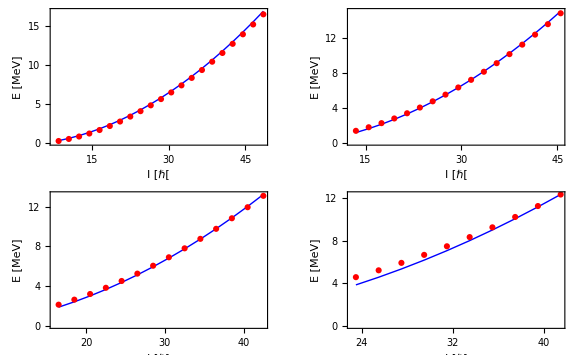

```mathematica
p1[exp_,th_]:=ListPlot[{exp,th},Frame->True,Axes->False,Joined->{False,True},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotMarkers->{Automatic,None},FrameLabel->{"I [ℏ[","E [MeV]"},LabelStyle->{14,Bold,Black,FontFamily->"Times New Roman"}];
GraphicsGrid[{{p1[data1exp,data1th],p1[data2exp,data2th]}, 
 {p1[data3exp,data3th],p1[data4exp,data4th]}},Frame->None,ImageSize->Large]
```